### Speed of a Random walk

```mathematica
L=21;
```

```mathematica
M=Table[If[Abs[i-j]<= 1, If[i==j, If[i==1 || i==L, -1,-2], 1], 0],{i, 1, L}, {j, 1, L}];
Val = Eigenvalues[M]//N;
Vec = Eigenvectors[Transpose[M]]//N;
Sol = Solve[Table[If[i==Ceiling[L/2], 1, 0], {i, 1, L}]==Sum[c[k] Vec[[k]], {k, 1, L}], Table[c[k], {k, 1, L}] ];
Coeff = Table[Sol[[1]][[i]][[2]], {i, 1, L}];
```

```mathematica
Prob[t_]:=Sum[Coeff[[k]] Vec[[k]] Exp[Val[[k]] t], {k, 1, L}]
```

```mathematica
Prob[0]
```

{2.22045×10^-16,2.08167×10^-17,-5.55112×10^-17,-4.16334×10^-17,-1.11022×10^-16,1.73472×10^-16,5.55112×10^-17,-6.93889×10^-17,1.11022×10^-16,-1.66533×10^-16,1.,-1.66533×10^-16,-3.33067×10^-16,-9.71445×10^-17,-1.38778×10^-16,-3.46945×10^-17,-4.16334×10^-17,-8.32667×10^-17,-1.38778×10^-16,-2.08167×10^-17,6.93889×10^-17}

```mathematica
plot =Flatten[Table[{k, t, Prob[t][[k]]}, {k ,1, L}, {t, 0, 20, 1}],1];
```

```mathematica
ListPlot3D[plot, PlotRange->All]
```

-Graphics3D-

```mathematica
Eval[t_]:= Sum[k Prob[t][[k]], {k, 1, L}];
```

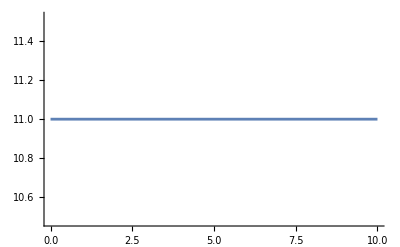

```mathematica
Plot[Eval[t], {t, 0, 10}]
```

```mathematica
SD[t_]:= (Sum[k^2 Prob[t][[k]], {k, 1, L}] - Eval[t]^2)^(1/2);
```

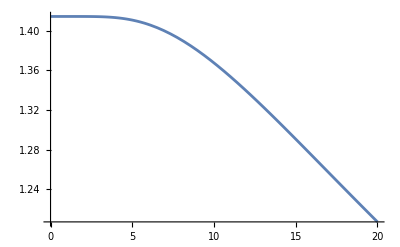

```mathematica
Plot[SD[t]/t^(1/2), {t, 0, 20}, PlotRange->Full]
```

```mathematica
N[√2]
```

1.41421

### Speed of a Random walk

```mathematica
L=21;
J=2;
```

```mathematica
M=Table[If[Abs[i-j]<= 1, If[i==j, If[i==1 || i==L, -J,-2 J], J], 0],{i, 1, L}, {j, 1, L}];
Val = Eigenvalues[M]//N;
Vec = Eigenvectors[Transpose[M]]//N;
Sol = Solve[Table[If[i==Ceiling[L/2], 1, 0], {i, 1, L}]==Sum[c[k] Vec[[k]], {k, 1, L}], Table[c[k], {k, 1, L}] ];
Coeff = Table[Sol[[1]][[i]][[2]], {i, 1, L}];
```

```mathematica
Prob[t_]:=Sum[Coeff[[k]] Vec[[k]] Exp[Val[[k]] t], {k, 1, L}]
```

```mathematica
Prob[0]
```

{2.22045×10^-16,2.08167×10^-17,-5.55112×10^-17,-4.16334×10^-17,-1.11022×10^-16,1.73472×10^-16,5.55112×10^-17,-6.93889×10^-17,1.11022×10^-16,-1.66533×10^-16,1.,-1.66533×10^-16,-3.33067×10^-16,-9.71445×10^-17,-1.38778×10^-16,-3.46945×10^-17,-4.16334×10^-17,-8.32667×10^-17,-1.38778×10^-16,-2.08167×10^-17,6.93889×10^-17}

```mathematica
plot =Flatten[Table[{k, t, Prob[t][[k]]}, {k ,1, L}, {t, 0, 20, 1}],1];
```

```mathematica
ListPlot3D[plot, PlotRange->All]
```

-Graphics3D-

```mathematica
Eval[t_]:= Sum[k Prob[t][[k]], {k, 1, L}];
```

```mathematica
Plot[Eval[t], {t, 0, 10}]
```

-Graphics-

```mathematica
SD[t_]:= (Sum[k^2 Prob[t][[k]], {k, 1, L}] - Eval[t]^2)^(1/2);
```

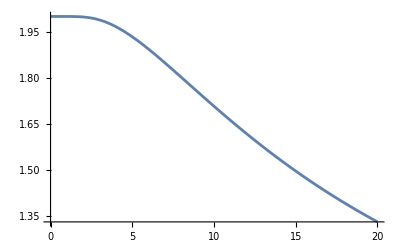

```mathematica
Plot[SD[t]/t^(1/2), {t, 0, 20}, PlotRange->Full]
```

```mathematica
N[√(2J)]
```

2.